```mathematica
ClearAll[x0,r1,r2]
```

### Part 2a

```mathematica
Module[{r1,r2},μ=0.01215;
xL1=0.8369157276;
r1=xL1+μ;        (*distance to Earth*)
r2=(1-μ)-xL1;
Ωxx=1+2*((1-μ)/r1^3+μ/r2^3);
Ωyy=1-((1-μ)/r1^3+μ/r2^3);
b=4-Ωxx-Ωyy;
c=Ωxx*Ωyy;
λ2roots=Solve[λ^4+b*λ^2+c==0,λ];
a={{0,0,1,0},{0,0,0,1},{Ωxx,0,0,2},{0,Ωyy,-2,0}};
T = Transpose[Eigenvectors[a]]//Chop;
diag=Inverse[T].a.T//Chop;
z0={0,0,0.01,0.01};
linic=T.z0//Chop//FullSimplify;
ω= Im[diag[[3,3]]];
tp=(2π)/ω;
linic[[1]] = linic[[1]]+xL1
]
DU=384400;
```

0.839031

```mathematica
linic
```

{0.839031,0,0,-0.0177086}

### Part 2b

```mathematica
F[x_,y_,vx_,vy_]:={x-((1-μ)*(x+μ))/r1[x,y]^3-(μ*(x+μ-1))/r2[x,y]^3+2 vy,-2 vx+y-((1-μ)*y)/r1[x,y]^3-(μ*y)/r2[x,y]^3}
r1[x_,y_]:=Sqrt[(x+μ)^2+y^2];
r2[x_,y_]:=Sqrt[(x-(1-μ))^2+y^2]
trajectory=ParametricNDSolve[{x''[t]==F[x[t],y[t],x'[t],y'[t]][[1]] ,y''[t]==F[x[t],y[t],x'[t],y'[t]][[2]],x[0]==x0,y[0]==y0,x'[0]==vx0,y'[0]==vy0},{x,y},{t,0,10},{x0,y0,vx0,vy0}];
f[x_,y_,vx_,vy_]:= {vx,vy,F[x,y,vx,vy]}//Flatten
αs={x,y,vx,vy};
A[x_,y_,vx_,vy_]:=Evaluate[Table[D[f[x,y,vx,vy][[i]],α],{i,1,4},{α,αs}](*/.{Abs'[z_]Abs[z_]->z}*)]
Φ=Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]<>"[t]"],{i,4},{j,4}];
Φ0=Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]<>"[0]"],{i,4},{j,4}];
dΦdt=Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]<>"'[t]"],{i,4},{j,4}];
unknowns =Table[ToExpression["ϕ"<>ToString[i]<>ToString[j]],{i,4},{j,4}]//Flatten;
stmeq[x0_,y0_,vx0_,vy0_]:=(#==0)&/@Flatten[dΦdt-(A[x[x0,y0,vx0,vy0][t],y[x0,y0,vx0,vy0][t],x[x0,y0,vx0,vy0]'[t],y[x0,y0,vx0,vy0]'[t]]/.trajectory).Φ]
stmic = (#==0)&/@Flatten[Φ0-IdentityMatrix[4]];
stmfull[x0_,y0_,vx0_,vy0_]:=Join[stmeq[x0,y0,vx0,vy0],stmic]
```

```mathematica
stm[x0_?NumericQ,y0_?NumericQ,vx0_?NumericQ,vy0_?NumericQ,tf_?NumericQ]:=ArrayReshape[Through[NDSolve[stmfull[x0,y0,vx0,vy0],unknowns,{t,0,tf}][[1]][[All,2]][tf]],{4,4}]
```

```mathematica
stm[linic[[1]],linic[[2]],linic[[3]],linic[[4]],0.00000001]//MatrixForm
```

(1. | -1.23288×10^-24 | 1.×10^-8 | 1.×10^-16
-3.67443×10^-24 | 1. | -1.×10^-16 | 1.×10^-8
1.15765×10^-7 | -3.68025×10^-16 | 1. | 2.×10^-8
-1.09685×10^-15 | -4.28825×10^-8 | -2.×10^-8 | 1.)

```mathematica
error[{vy0_,tf_}]:= { y[linic[[1]], 0 , 0,vy0 ][tf] -0,x[linic[[1]], 0 , 0,vy0]'[tf]-0 }/.trajectory
```

```mathematica
Sensm[x0_,y0_,vx0_,vy0_,t_]:={{stm[x0,y0,vx0,vy0,t][[2,4]],y[x0,y0,vx0,vy0]'[t] },{stm[x0,y0,vx0,vy0,t][[3,4]], x[x0,y0,vx0,vy0]''[t]}}/.trajectory 
invsensm[{vy0_,tf_}]:= Inverse[Sensm[linic[[1]],linic[[2]],linic[[3]],vy0,tf]]
```

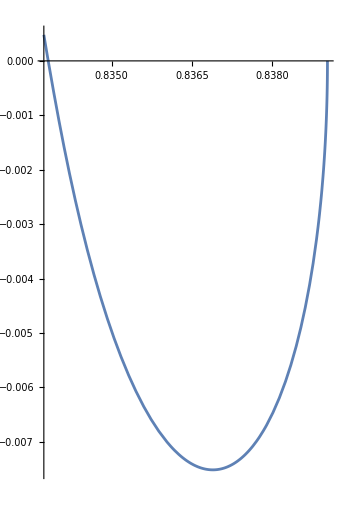

```mathematica
ParametricPlot[{x[linic[[1]],linic[[2]],linic[[3]],linic[[4]]][t],y[linic[[1]],linic[[2]],linic[[3]],linic[[4]]][t]}/.trajectory,{t,0,tp/2}]
```

```mathematica
n=100;
param = 0.2;
XState=ConstantArray[0,n];
ERR=ConstantArray[0,n];
B=ConstantArray[0,n];
XState[[1]] = {linic[[4]],tp/2};
ERR[[1]]=error[XState[[1]]];
B[[1]]=invsensm[XState[[1]]];
Dynamic[i]
```

```mathematica
For[i=1,i<n,i++,
XState[[i+1]]=XState[[i]]-param (B[[i]].ERR[[i]]);
ERR[[i+1]]=error[XState[[i+1]]];
B[[i+1]]=invsensm[XState[[i+1]]];
]
```

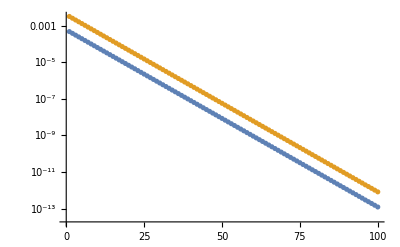

```mathematica
ListLogPlot[ERR//Transpose//Abs]
```

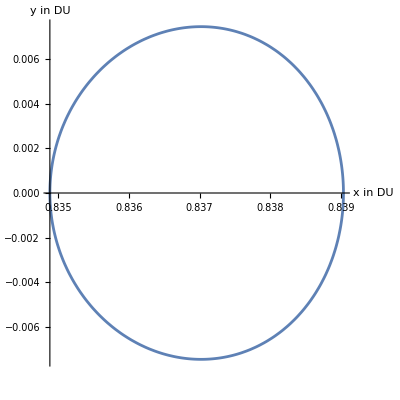

```mathematica
ParametricPlot[{x[linic[[1]],linic[[2]],linic[[3]],XState[[-1]][[1]]][t],y[linic[[1]],linic[[2]],linic[[3]],XState[[-1]][[1]]][t]}/.trajectory,{t,0,2*XState[[-1]][[2]] },AspectRatio->1,AxesLabel->{"x in DU","y in DU"}]
```

### Part 2c

```mathematica
errornew[x0_,{vy0_,tf_}]:= { y[x0, 0 , 0,vy0 ][tf] -0,x[x0, 0 , 0,vy0]'[tf]-0 }/.trajectory 
invsensmnew[x0_,{vy0_,tf_}]:= Inverse[Sensm[x0,linic[[2]],linic[[3]],vy0,tf]]
```

```mathematica
getdesign=Function[{x0,vy0,tf},Module[{Xstateold,ERRold,bold,Xstatenew, ERRnew,bnew,normerr,param =0.5},
Xstateold = {vy0,tf};
ERRold=errornew[x0,Xstateold];
bold=invsensmnew[x0,Xstateold];
normerr = 1;
While[normerr>10^-6,
Xstatenew=Xstateold-param (bold.ERRold);
ERRnew=errornew[x0,Xstatenew];
bnew=invsensmnew[x0,Xstatenew];
normerr = Norm[ERRnew];
Xstateold = Xstatenew;
ERRold = ERRnew;
bold=bnew;
];
Xstateold]
];
Ω[x_,y_]:=1/2(x^2+y^2)+((1-μ)/r1[x,y])+μ/r2[x,y]
v[vx_,vy_]:=Sqrt[vx^2+vy^2]
cfun[x_,y_,vx_,vy_]:=2 Ω[x,y]-v[vx,vy]^2
c=Apply[cfun,linic]
res={}
Dynamic[c]
```

3.18807

{}

```mathematica
linic
```

{0.625394,0,0,1.77086}

```mathematica
Module[{x0 = linic[[1]],y0=0,vx0=0,vy0=linic[[4]],tf =tp/2,Δx = 100/DU},
While[c>=3.04,
{vy0,tf} =getdesign[x0,vy0,tf];
res = Append[res,{x0,vy0,tf}];
c=cfun[x0,y0,vx0,vy0];
x0 =x0+Δx;
]
]
```

$Aborted

```mathematica
plot[pars_]:=ParametricPlot[{x[pars[[1]],0,0,pars[[2]]][t],y[pars[[1]],0,0,pars[[2]]][t]}/.trajectory,{t,0,2*pars[[3]] },AspectRatio->1,AxesLabel->{"x in DU","y in DU"}]
```

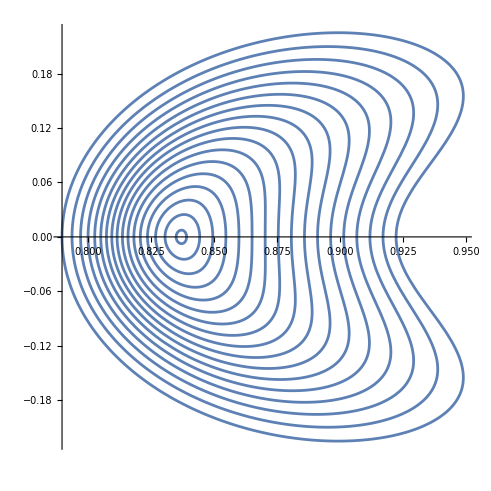

```mathematica
Show[plot/@Reverse[res[[1;;-1;;20]]]]
```